# Introdução ao Mathematica

Arquivo contendo alguns exemplos para montar arquivos no Mma
Cada delimitador tem uma função distinta
argumentos de função [], entre [] a variavel é definida com “_” 
listas: vetores, matrizes, tensores {}
agrupa ()
espaço no Mma signfica multiplicação
letras ou variaveis gregas podem ser obtidas com esc-letra-esc

```mathematica
SetDirectory[NotebookDirectory[]]
```

C:\Users\anton\OneDrive\Documentos\Wolfram Mathematica

```mathematica
FullForm[1231231231231231234534534/454549898]
```

Rational[615615615615615617267267,227274949]

```mathematica
FullForm[1231231231231231234534534/454549898.]
```

2.70868×10^15

```mathematica
f[x_, y_]:=Cos[ x y]
```

```mathematica
Plot3D[ f[x, y],{x, - Pi, Pi}, {y, -Pi, Pi}]
```

-Graphics3D-

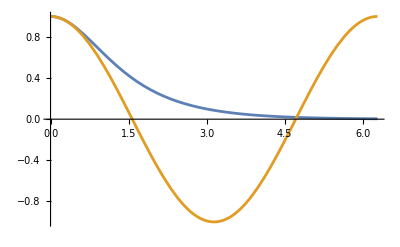

```mathematica
Plot[{1/Cosh[x],Cos[x]}, {x,0, 2 π }, PlotRange->All]
```

## Comparação entre os diferentes modelos de uma linha de transmissão

### quadripolo da linha curta

```mathematica
Qc[z_, ℓ_]:={{1, z ℓ},{0,1}}
```

```mathematica
(* dados retirados da tabela da EPE *)
z=0.1914+ⅉ*0.5014;
y =I 3.3018 10^-6;
compr=3  50.0;
Vn = 138
```

138

```mathematica
Zc=Sqrt[Im[z]/Im[y]]
```

389.688

```mathematica
Pn= Vn^2/Zc
```

48.8699

```mathematica
Ir = Pn/(Sqrt[3] Vn) 10^3
```

204.457

```mathematica
Vr = Vn 10^3;
```

```mathematica
MatrixForm[q1=Qc[z, compr]]
```

(1 | 28.71+75.21 ⅈ
0 | 1)

```mathematica
{vs, is}=q1.{Vr/Sqrt[3], Ir}
```

{85544.3+15377.2 ⅈ,204.457+0. ⅈ}

```mathematica
Vs= vs/10^3 Sqrt[3]
```

148.167+26.6341 ⅈ

```mathematica
ps= 3 vs Conjugate[is]
```

5.24704×10^7+9.43192×10^6 ⅈ

```mathematica
Re[ps/10^6]/Pn
```

1.07367

```mathematica
Arg[vs]/π 180
```

10.1905

### quadripolo da linha longa

```mathematica
compr
```

150.

```mathematica
Ql[z_, y_, ℓ_]:=Module[{γ=Sqrt[z y], zc=Sqrt[z/ y]},
{{Cosh[γ ℓ], zc Sinh[γ ℓ]},{1/zc Sinh[γ ℓ],Cosh[γ ℓ]}}]
```

```mathematica
MatrixForm[q2=Ql[z,y,compr]]
```

(0.981425+0.00706554 ⅈ | 28.3545+74.8116 ⅈ
-1.16936×10^-6+0.0004922 ⅈ | 0.981425+0.00706554 ⅈ)

```mathematica
MatrixForm[Qc[z, compr]]
```

(1 | 28.71+75.21 ⅈ
0 | 1)

```mathematica
{vs2, is2}=q2.{Vr/Sqrt[3], Ir}
```

{83991.6+15858.7 ⅈ,200.566+40.6603 ⅈ}

```mathematica
3 vs2 Conjugate[is2]
```

5.2472×10^7-703246. ⅈ

```mathematica
is/is2
```

0.979158-0.198503 ⅈ

```mathematica
Arg[is]/Arg[is2]
```

0.

```mathematica
Arg[vs]/Arg[vs2]
```

0.953069

### Montando o Quadripolo da Linha Média -- circuito π Nominal

para evitar problemas com os valores numericos anteriores -- mate o Kernel antes de executar as células abaixo

```mathematica
qd[y_]={{1,0},{y,1}}
```

{{1,0},{y,1}}

```mathematica
qs[z_]={{1,z},{0,1}}
```

{{1,z},{0,1}}

```mathematica
qd[y1 ℓ/2].qs[z1 ℓ].qd[y1 ℓ/2]
```

{{1+1/2 y1 z1 ℓ^2,z1 ℓ},{(y1 ℓ)/2+1/2 y1 ℓ (1+1/2 y1 z1 ℓ^2),1+1/2 y1 z1 ℓ^2}}

```mathematica
Series[Cosh[x], {x,0,2}]//Normal
```

1+x^2/2

```mathematica
Series[Sinh[x], {x,0,2}]//Normal
```

x